```mathematica
file=URLDownload["https://img1.dxycdn.com/2020/0203/561/3394511511061134801-135.png"]
```

```mathematica
Import[file,{"PNG","XMP"}]
```

```mathematica
Import[file,{"PNG","Comments"}]
```

```mathematica
data[All,"AdministrativeDivision"]
```

```mathematica
Hyperlink["https://github.com/login/oauth/authorize?client_id=arnoudbuzing&redirect_uri=https://www.wolfram.com"]
```

```mathematica
i=1;
more=True;
result={};
While[more,
Pause[1];
Echo[i];
search=URLRead["https://api.github.com/search/repositories?page="<>ToString[i]<>"&q=coronavirus"];
json=ImportByteArray[search["BodyByteArray"],"RawJSON"];
Echo[Length[json]];
If[Length[json]=!=3,Abort[]];
AppendTo[result,json["items"]];
If[Length[json["items"]]>0,Null,more=False];
i++
];
```

1

3

2

3

3

3

4

3

5

3

6

3

7

3

8

2

$Aborted

```mathematica
Length[Flatten[result]]
```

210

```mathematica
ds=Dataset[Map[<|"name"->#["name"],"owner"->#["owner"]["login"]|>&,Flatten[result]]]
```

```mathematica
json=ImportByteArray[search["BodyByteArray"],"RawJSON"];
```

```mathematica
json["items"]//Length
```

```mathematica
gettags[assoc_]:=Module[{repo,owner,url,tags},
Pause[.1];
repo=assoc["name"];
owner=assoc["owner"];
Echo[url=URL["https://api.github.com/repos/"<>owner<>"/"<>repo<>"/topics"]];
tags=URLRead[HTTPRequest[url,<|"Headers"->{"Accept"->"application/vnd.github.mercy-preview+json","Authorization"->"token "<>token}|>]];
tags=ImportByteArray[tags["BodyByteArray"],"RawJSON"];
<|"owner"->owner,"repo"->repo,"tags"->tags["names"]|>
]
```

```mathematica
Map[f,Take[ds,3]]
```

```mathematica
result2=Map[gettags,ds];
```

URL[https://api.github.com/repos/globalcitizen/2019-wuhan-coronavirus-data/topics]

URL[https://api.github.com/repos/nextstrain/ncov/topics]

URL[https://api.github.com/repos/839Studio/Novel-Coronavirus-Updates/topics]

URL[https://api.github.com/repos/ncovis/choropleth/topics]

URL[https://api.github.com/repos/docligot/coronatracker-analytics/topics]

URL[https://api.github.com/repos/AaronWard/coronavirus-analysis/topics]

URL[https://api.github.com/repos/hysios/coronavirus/topics]

URL[https://api.github.com/repos/lbj96347/2020-new-coronavirus-live-map/topics]

URL[https://api.github.com/repos/TIT-Lab/coronavirus-map/topics]

URL[https://api.github.com/repos/YiranJing/Coronavirus-Epidemic-2019-nCov/topics]

URL[https://api.github.com/repos/vilaca/wuhan-coronavirus-outbreak/topics]

URL[https://api.github.com/repos/artic-network/artic-ncov2019/topics]

URL[https://api.github.com/repos/antonlukin/2019-nCoV/topics]

URL[https://api.github.com/repos/dreamerjackson/coronavirus/topics]

URL[https://api.github.com/repos/chrism0dwk/wuhan/topics]

URL[https://api.github.com/repos/HopkinsIDD/ncov_incubation/topics]

URL[https://api.github.com/repos/MeoncStudio/Anti_2019-ncoV/topics]

URL[https://api.github.com/repos/DnCov/transparent-info/topics]

URL[https://api.github.com/repos/alext234/coronavirus-stats/topics]

URL[https://api.github.com/repos/Kyald1412/CoronaVirus-2019-nCoV-Live-Tracking/topics]

URL[https://api.github.com/repos/iidx/corona-tracker/topics]

URL[https://api.github.com/repos/nextstrain/cov/topics]

URL[https://api.github.com/repos/Xetera/corona/topics]

URL[https://api.github.com/repos/pdtyreus/coronavirus-ds/topics]

URL[https://api.github.com/repos/instafluff/Coronavirus/topics]

URL[https://api.github.com/repos/WeileiZeng/red-cross/topics]

URL[https://api.github.com/repos/WuhanZhuRong/DonationChannel/topics]

URL[https://api.github.com/repos/Laeyoung/Wuhan-Coronavirus-API/topics]

URL[https://api.github.com/repos/aitahtman/coronavirus/topics]

URL[https://api.github.com/repos/the-robot/corona-bot/topics]

URL[https://api.github.com/repos/jarekpelczynski/ncov-data-fetcher/topics]

URL[https://api.github.com/repos/avischiffmann/Coronavirus-Dashboard/topics]

URL[https://api.github.com/repos/sijiali57/coronavirus_data/topics]

URL[https://api.github.com/repos/kevinlu1248/corona/topics]

URL[https://api.github.com/repos/labsletemps/coronavirus-world-map/topics]

URL[https://api.github.com/repos/xcv58/Coronavirus/topics]

URL[https://api.github.com/repos/JordanMicahBennett/SMART-CORONA_VIRUS_DETECTOR/topics]

URL[https://api.github.com/repos/yitao94/2019-nCoV/topics]

URL[https://api.github.com/repos/WebDevSimplified/Coronavirus-Chrome-Extension/topics]

URL[https://api.github.com/repos/fangohr/coronavirus-2020/topics]

URL[https://api.github.com/repos/JunjieZhouwust/Coronavirus-Estimation/topics]

URL[https://api.github.com/repos/etchorigin/ncov2019/topics]

URL[https://api.github.com/repos/arnoudbuzing/wolfram-coronavirus/topics]

URL[https://api.github.com/repos/kaiyz/corona/topics]

URL[https://api.github.com/repos/Cyberist-Edgar/2020-novel-coronavirus/topics]

URL[https://api.github.com/repos/coddec/2020-new-coronavirus/topics]

URL[https://api.github.com/repos/mshyun/coronavirus/topics]

URL[https://api.github.com/repos/viral-coronavirus-dev/viral-coronavirus/topics]

URL[https://api.github.com/repos/Sviper-07/CoronavirusOdesseyRepo/topics]

URL[https://api.github.com/repos/muditham90/viral-coronavirus/topics]

URL[https://api.github.com/repos/netqyq/coronavirus-stat/topics]

URL[https://api.github.com/repos/mudiant/viral-coronavirus/topics]

URL[https://api.github.com/repos/iPomme/GameJame2020/topics]

URL[https://api.github.com/repos/lbj96347/2020-new-coronavirus-info-crawler/topics]

URL[https://api.github.com/repos/chunyeow/dash-coronavirus/topics]

URL[https://api.github.com/repos/mcodz/coronavirus/topics]

URL[https://api.github.com/repos/dranoer/corona/topics]

URL[https://api.github.com/repos/SpencerAung/coronavirus-info/topics]

URL[https://api.github.com/repos/burgess/2019-nCoV/topics]

URL[https://api.github.com/repos/ivan-iliev/mc-2d/topics]

URL[https://api.github.com/repos/POGE0124/Coronavirus_quantity_prediction/topics]

URL[https://api.github.com/repos/joshuaferr1s/coronavirus/topics]

URL[https://api.github.com/repos/stephan227/coronavirus-data-hq/topics]

URL[https://api.github.com/repos/lina/lina.github.io/topics]

URL[https://api.github.com/repos/ricosmall/2019-ncov/topics]

URL[https://api.github.com/repos/kealyn/Wuhan2019/topics]

URL[https://api.github.com/repos/iuming/Coronavirus/topics]

URL[https://api.github.com/repos/piscium2010/coronavirus-map/topics]

URL[https://api.github.com/repos/aknow2/situation-coronavirus/topics]

URL[https://api.github.com/repos/htso/Coronavirus_Epidemic/topics]

URL[https://api.github.com/repos/widscommunityorg/CoronaV_Challenge/topics]

URL[https://api.github.com/repos/kianweelee/Data-Visualisation--Coronavirus-confirmed-cases/topics]

URL[https://api.github.com/repos/eragmus/2019ncov/topics]

URL[https://api.github.com/repos/aliciawyy/coronavirus-outbreak-log/topics]

URL[https://api.github.com/repos/biomedontology/cido/topics]

URL[https://api.github.com/repos/epiforecasts/WuhanSeedingVsTransmission/topics]

URL[https://api.github.com/repos/sgfm/CoronavirusVisualization/topics]

URL[https://api.github.com/repos/RuyiLi/coronatracker/topics]

URL[https://api.github.com/repos/yx-z/wuhan/topics]

URL[https://api.github.com/repos/SuperDiscovery/NCP-Model/topics]

URL[https://api.github.com/repos/JenQian/coronavirus-data-ETL/topics]

URL[https://api.github.com/repos/SWKeenan/coronavirusAPI/topics]

URL[https://api.github.com/repos/itsyaoyu/wuhan_coronavirus/topics]

URL[https://api.github.com/repos/sanghy/epidemicsituation2020/topics]

URL[https://api.github.com/repos/QMHTMY/Coronavirus/topics]

URL[https://api.github.com/repos/audreyqyfu/wuhancov/topics]

URL[https://api.github.com/repos/ergodiclife/wuhan-coronavirus/topics]

URL[https://api.github.com/repos/ljnicol/coronavirus_viz/topics]

URL[https://api.github.com/repos/ShuuTsubaki/Wuhan-Coronavirus-Even-Timeline/topics]

URL[https://api.github.com/repos/MaBeuLux88/coronavirus-mongodb/topics]

URL[https://api.github.com/repos/lukas-jue/coronavirus/topics]

URL[https://api.github.com/repos/sdwfrost/mers-analysis/topics]

URL[https://api.github.com/repos/donpaul999/coronavirusMap/topics]

URL[https://api.github.com/repos/KezhiLi/Wuhan_Coronavirus/topics]

URL[https://api.github.com/repos/ykl124/Shanghai2020/topics]

URL[https://api.github.com/repos/elvinaqa/The-Rise-of-CoronaVirus/topics]

URL[https://api.github.com/repos/xstarseed/coronavirus/topics]

URL[https://api.github.com/repos/martinedoesgis/novel-coronavirus/topics]

URL[https://api.github.com/repos/choderalab/coronavirus/topics]

URL[https://api.github.com/repos/JackJoeng/coronavirus/topics]

URL[https://api.github.com/repos/jubayer-hossain/CoronavirusTracking/topics]

URL[https://api.github.com/repos/hriewe/CoronavirusTracker/topics]

URL[https://api.github.com/repos/SuriousCompany/CoronavirusObserver/topics]

URL[https://api.github.com/repos/blowsys/Coronavirus/topics]

URL[https://api.github.com/repos/yuhanbae06/coronavirus/topics]

URL[https://api.github.com/repos/kaixin1976/coronavirus/topics]

URL[https://api.github.com/repos/notfree/Coronavirus/topics]

URL[https://api.github.com/repos/Schukerz/Coronavirus/topics]

URL[https://api.github.com/repos/nurulc/coronavirus/topics]

URL[https://api.github.com/repos/perlatex/2019-nCoV/topics]

URL[https://api.github.com/repos/liu-zoe/wuhancv/topics]

URL[https://api.github.com/repos/qingzma/coronavirusMonitor/topics]

URL[https://api.github.com/repos/bahe007/CoronaTracker/topics]

URL[https://api.github.com/repos/FrankChen021/2019-ncov/topics]

URL[https://api.github.com/repos/PengKuang/wuhan2020-oversea/topics]

URL[https://api.github.com/repos/liuyangly25/infection_prediction/topics]

URL[https://api.github.com/repos/PranavPable/2019-n-CoV-Virus-Dashboard/topics]

URL[https://api.github.com/repos/apex-stack/true-coronavirus/topics]

URL[https://api.github.com/repos/SuperSt3ve/coronavirus/topics]

URL[https://api.github.com/repos/MarGonz7/coronavirus/topics]

URL[https://api.github.com/repos/cfshi/coronavirus/topics]

URL[https://api.github.com/repos/TheGodOfHuaji/Coronavirus/topics]

URL[https://api.github.com/repos/Dork3yyyy/coronavirus/topics]

URL[https://api.github.com/repos/joaogrosso/Coronavirus/topics]

URL[https://api.github.com/repos/itoic/coronavirus/topics]

URL[https://api.github.com/repos/toyourheart163/coronavirus/topics]

URL[https://api.github.com/repos/finateautomata/Coronavirus/topics]

URL[https://api.github.com/repos/lprone/coronavirus/topics]

URL[https://api.github.com/repos/ozpv/Coronavirus/topics]

URL[https://api.github.com/repos/dizzySummer/coronavirusRealTimeData/topics]

URL[https://api.github.com/repos/flyffast/CoronavirusHackUCI/topics]

URL[https://api.github.com/repos/leonluleonlu/2019-nCoV_Donation/topics]

URL[https://api.github.com/repos/eebrown/data2019nCoV/topics]

URL[https://api.github.com/repos/mot200286mot/CoronaVirus/topics]

URL[https://api.github.com/repos/bovinemagnet/coronavirus-neo4j/topics]

URL[https://api.github.com/repos/kalzeo/nCoV-API/topics]

URL[https://api.github.com/repos/casperbrike/corona_bot/topics]

URL[https://api.github.com/repos/bwanglzu/404-not-found/topics]

URL[https://api.github.com/repos/ThinkGeo/Coronavirus-Wuhan-nCoV-2019/topics]

URL[https://api.github.com/repos/nyem69/coronavirus_dashboard/topics]

URL[https://api.github.com/repos/ncoronavirus/Toronto2020/topics]

URL[https://api.github.com/repos/donghoony1/2019-nCoV/topics]

URL[https://api.github.com/repos/CoDeRgAnEsh/nCoV-2019/topics]

URL[https://api.github.com/repos/chunyeow/coronavirus-crawling/topics]

URL[https://api.github.com/repos/JakeJing/wuhan-coronavirus/topics]

URL[https://api.github.com/repos/sungml92/2019-nCov/topics]

URL[https://api.github.com/repos/changbing2019/lstm4ncor/topics]

URL[https://api.github.com/repos/nickofc/coronavirus/topics]

URL[https://api.github.com/repos/wonyoungchoiseoul/coronavirus/topics]

URL[https://api.github.com/repos/teddylun/coronavirus/topics]

URL[https://api.github.com/repos/alamjane/Coronavirus/topics]

URL[https://api.github.com/repos/johnmelodyme/CoronaVirus/topics]

URL[https://api.github.com/repos/themarcusaurelius/coronaVirus/topics]

URL[https://api.github.com/repos/sta199-sp20-002/appex-04-coronavirus/topics]

URL[https://api.github.com/repos/TheCode-Jedi/CoronaVirus-MD/topics]

URL[https://api.github.com/repos/DnCov/DnCov/topics]

URL[https://api.github.com/repos/yarfer/coronavirus/topics]

URL[https://api.github.com/repos/Yuriyama/Coronavirus/topics]

URL[https://api.github.com/repos/GHumorBS/Coronavirus/topics]

URL[https://api.github.com/repos/colortail/coronavirus/topics]

URL[https://api.github.com/repos/HardWorkerIlya/coronavirus/topics]

URL[https://api.github.com/repos/Dajnowicz/CoronaVirus/topics]

URL[https://api.github.com/repos/escudero/coronavirus/topics]

URL[https://api.github.com/repos/NarekSag/CoronaVirus/topics]

URL[https://api.github.com/repos/henry123i/coronavirus/topics]

URL[https://api.github.com/repos/diehard04/coronavirus/topics]

URL[https://api.github.com/repos/daniel2231/coronavirusmap/topics]

URL[https://api.github.com/repos/kalzeo/CoronavirusWebsiteTracker/topics]

URL[https://api.github.com/repos/guptaekarigar/coronavirustracker/topics]

URL[https://api.github.com/repos/nnikniL/2019-nCoV_Notes/topics]

URL[https://api.github.com/repos/Ruchit007/CoronaVirus/topics]

URL[https://api.github.com/repos/Koohoko/Coronavirus_Bayseian_Modelling/topics]

URL[https://api.github.com/repos/PratirupG/coronavirusanalysis/topics]

URL[https://api.github.com/repos/nerocui/coronavirustracker/topics]

URL[https://api.github.com/repos/EthanGeekFan/nCoV/topics]

URL[https://api.github.com/repos/WooilJeong/novel_coronavirus/topics]

URL[https://api.github.com/repos/damonYuan/ncov-api-k8s/topics]

URL[https://api.github.com/repos/davy868/propagation-model-for-2019-nCov/topics]

URL[https://api.github.com/repos/hernanmd/nCoV-2019/topics]

URL[https://api.github.com/repos/aejsong/novel-coronavirus-exploratory-analysis/topics]

URL[https://api.github.com/repos/Gazerbeamco/coronavirus/topics]

URL[https://api.github.com/repos/143034/-coronavirus-/topics]

URL[https://api.github.com/repos/karolkolodziej/coronavirus/topics]

URL[https://api.github.com/repos/larsgimse/coronaviruslamp/topics]

URL[https://api.github.com/repos/joshualeung/wuhan-coronavirus/topics]

URL[https://api.github.com/repos/ctedijanto/coronavirus-seasonality/topics]

URL[https://api.github.com/repos/jwktls/Coronavirus_ios/topics]

URL[https://api.github.com/repos/optoisolated/coronavirus-stats/topics]

URL[https://api.github.com/repos/mrmattwright-inc/coronavirus-virus/topics]

URL[https://api.github.com/repos/maksim72/coronavirus-website/topics]

URL[https://api.github.com/repos/PatornJantara/coronavirus-detection/topics]

URL[https://api.github.com/repos/ExtReMLapin/gmod_coronavirus/topics]

URL[https://api.github.com/repos/catofsof/coronavirus-api/topics]

URL[https://api.github.com/repos/Sun2yKid/Anti-2019-nCoV/topics]

URL[https://api.github.com/repos/epignatelli/coronavirus-infographics/topics]

URL[https://api.github.com/repos/developers-arm/Coronavirus-things/topics]

URL[https://api.github.com/repos/HesterLim/coronavirus-analysis/topics]

URL[https://api.github.com/repos/lichader/coronavirus-bot/topics]

URL[https://api.github.com/repos/yongjun21/wuhan-coronavirus/topics]

URL[https://api.github.com/repos/android-apps-apk/coronavirus-protect/topics]

URL[https://api.github.com/repos/edwardcooper/wuhan-virus-paper/topics]

URL[https://api.github.com/repos/thiennv2896/Corona-Monitor/topics]

URL[https://api.github.com/repos/changbing2019/LSTM4Coronavirusprediction/topics]

URL[https://api.github.com/repos/Olivine-Ryo/coronavirus_map/topics]

URL[https://api.github.com/repos/nancyyanyu/coronavirus_project/topics]

URL[https://api.github.com/repos/A-Yifeng/wuhan-coronavirus/topics]

URL[https://api.github.com/repos/imsoncod/Coronavirus-Map/topics]

URL[https://api.github.com/repos/nyem69/coronavirus_data/topics]

URL[https://api.github.com/repos/smorfopoulou/coronavirus_genbank/topics]

URL[https://api.github.com/repos/andrewadiletta/coronavirus_gizmo/topics]

```mathematica
Flatten[Normal[result2[All,"tags"]]]
```

{wuhan,2019ncov,coronavirus,virology,2019-ncov,pathogens,viruses,pandemic,opendata,epedemiology,epedemic,wuhan,coronavirus,coronavirus-real-time,2019-ncov,2019ncov,ncov,2020ncov,wuhan-virus,china,virus,pandemic,coronavirus,ncov-2019,scrapy,webcrawler,2019-ncov,statistical-models,visualization,python,coronavirus,coronavirus-real-time,epidemic-model,wuhan-coronavirus-outbreak,coronavirus,2019-ncov,wuhan,coronavirus,lancaster-university,epidemic,epidemic-model,data-science,jupyter-notebook,coronavirus,data-mining,kotlin,android,coronavirus,coronavirus,2019-ncov,corona-tracker,medical,telegram-bot,coronavirus,jupyter-notebook,geopandas,data-science,red-cross,github-pages,coronavirus,wuhan,coronavirus,2019-ncov,coronavirus,mapbox-gl,disease,coronavirus,coronavirus-globaloutbreak,coronavirus-real-time,wuhan-pneumonia,wuhan-coronavirus-outbreak,telegram-bot,coronavirus,mathematica,wolfram-language,data-science,new-coronavirus,pneumonia,wuhan,info-websites,information,wuhan-pneumonia,wuhan-coronavirus,coronavirus-globaloutbreak,novel-coronavirus,real-time-map,wuhan-coronavirus-outbreak,2019-ncov,nvoc,coronavirus-maps,coronavirus-tracking,coronavirus,coronavirus-real-time,coronavirus-info,coronavirus-websites,coronavirus-real-time,coronavirus,wuhan-pneumonia,wuhan-coronavirus-outbreak,epidemics,prediction-model,r,regression-models,ncov,ncov-data-visual,rstats,rstats-package,corona,python,pandas,numpy,matplotlib,seaborn,r,coronavirus,rpackage,data,epidemiology,ncov,ncov-2019,dataset,corona,wuhan,wuhan-coronavirus,ncov-2019,ncov,wuhan-virus,data-analysis,statistics,2019-ncov,wuhan,coronavirus,sars,kubernetes,wuhan,api,ncov-2019,bioinformatics,smalltalk,coronavirus,coronavirus,coronavirus-tracking,coronavirus}

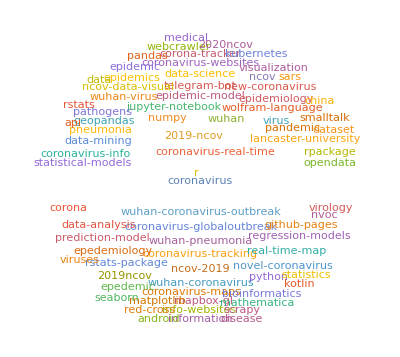

```mathematica
WordCloud[%]
```

```mathematica
Export["D:\\git\\wolfram-coronavirus\\github-topic-wordcloud.png",Out[215]]
```

D:\git\wolfram-coronavirus\github-topic-wordcloud.png

```mathematica
Length[json["items"]]
```

```mathematica
items=json["items"];
```

```mathematica
Table[gettags[json,i],{i,30}]//Dataset
```

```mathematica
Keys[json]
```

```mathematica
json["incomplete_results"]
```

```mathematica
json["items"]//Length
```

```mathematica
json
```